# PRACTICAL 5 : SIMULTANEOUS DIFFERENTIAL EQUATION

### A two dimensional linear system is a system of the form : dx/dt = a x + by dy/dt= c x + dy where a,b,c and d are parameters. This system can be written in matrix form as X = AX, where A = ( a b and X = ( x c d ) y ) The solutions of X = AX can be visualized as trajectories moving on the x- y plane called the phase plane.

## QUes 1 : Solve the following system of equations : dx/dt = -3x- y dy/dt = x-3y

```mathematica
eq1= {x'[t] == -3*x[t]-y[t], y'[t] == -3y[t] -x[t]}
```

{x'[t]==-3 x[t]-y[t],y'[t]==-x[t]-3 y[t]}

```mathematica
sol= DSolve[eq1, {y[t], x[t]}, t]
```

{{x[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
tabx= Table[x[t] /. sol[[1,1]]/. {C[1]-> i, C[2]-> j}, {i,-1,0}, {j,0,1}]//Flatten
```

{-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))}

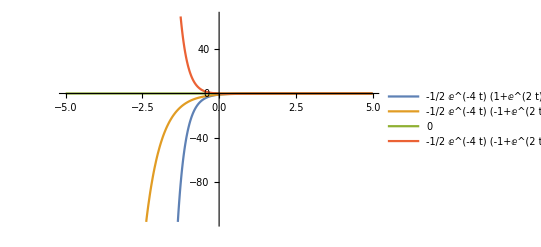

```mathematica
Plot[Evaluate[tabx], {t,-5,5}, PlotLegends->"Expressions"]
```

```mathematica
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i , C[2]-> j}, {i,-1,0}, {j,0,1}]//Flatten
```

{1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,1/2 ⅇ^(-4 t) (1+ⅇ^(2 t))}

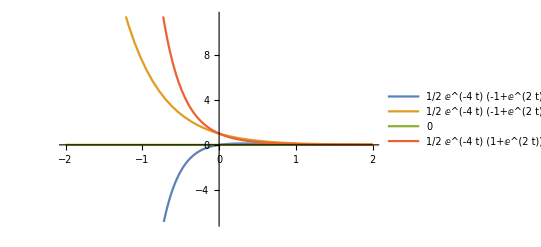

```mathematica
Plot[Evaluate[taby], {t,-2,2}, PlotLegends->"Expressions"]
```

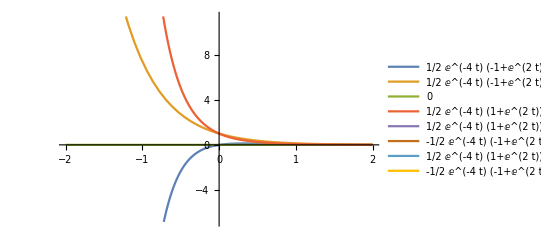

```mathematica
Plot[Evaluate[{taby,tabx}], {t,-2,2}, PlotLegends->"Expressions"]
```

## Ques 2 : Solve the following system of equations : dx/dt = y dy/dt = 6x- y with initial condition x(0)= 1, y(0) = -2

```mathematica
eq2={{x'[t]==y[t], y'[t]==-y[t]+6x[t]}, x[0]==1, y[0]==-2}
```

{{x'[t]==y[t],y'[t]==6 x[t]-y[t]},x[0]==1,y[0]==-2}

```mathematica
DSolve[eq2, {x[t], y[t]}, t]
```

{{x[t]→1/5 ⅇ^(-3 t) (4+ⅇ^(5 t)),y[t]→2/5 ⅇ^(-3 t) (-6+ⅇ^(5 t))}}

```mathematica
{xsol[t_], ysol[t_]}= ExpandAll[{x[t], y[t]}/.Flatten[DSolve[eq2, {x[t], y[t]}, t]]]
```

{(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5,-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5}

```mathematica
xsol[t]
```

(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5

```mathematica
ysol[t]
```

-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5

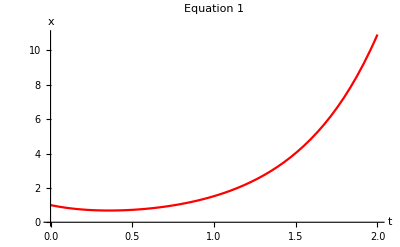

```mathematica
plot1=Plot[xsol[t], {t,0,2}, AxesLabel->{"t", "x"}, PlotLabel->"Equation 1", PlotStyle->{Red}]
```

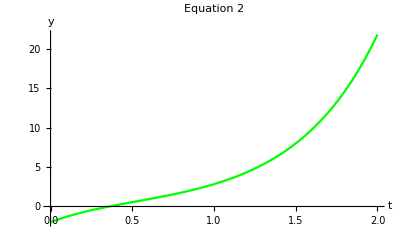

```mathematica
plo2=Plot[ysol[t], {t,0,2}, AxesLabel->{"t", "y"}, PlotLabel->"Equation 2", PlotStyle->{Green}]
```

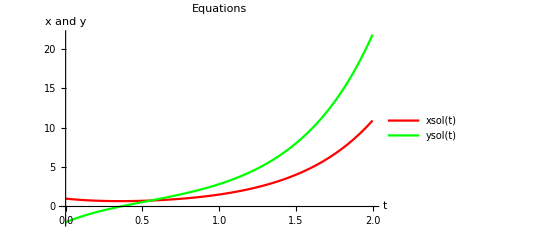

```mathematica
Plot[{xsol[t], ysol[t]}, {t,0,2}, AxesLabel->{"t","x and y" }, PlotLabel->"Equations", PlotStyle->{Red, Green}, PlotLegends->"Expressions"]
```

## Solve the following Simultaneous DE and hence plot the solutions : Ques 3 : dx/dt = 5x - 2y dy/dt= 4x-y

```mathematica
eq1={x'[t]==5*x[t]-2*y[t], y'[t]== -y[t] +4*x[t]}
```

{x'[t]==5 x[t]-2 y[t],y'[t]==4 x[t]-y[t]}

```mathematica
sol=DSolve[eq1, {y[t], x[t]}, t]
```

{{x[t]→ⅇ^t (-1+2 ⅇ^(2 t)) C[1]-ⅇ^t (-1+ⅇ^(2 t)) C[2],y[t]→2 ⅇ^t (-1+ⅇ^(2 t)) C[1]-ⅇ^t (-2+ⅇ^(2 t)) C[2]}}

```mathematica
tabx=Table[x[t]/.sol[[1,1]]/. {C[1]-> i, C[2]-> j}, {i,-1,0}, {j,0,1}]//Flatten
```

{-ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+ⅇ^(2 t))-ⅇ^t (-1+2 ⅇ^(2 t)),0,-ⅇ^t (-1+ⅇ^(2 t))}

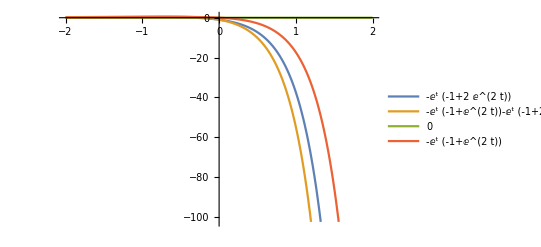

```mathematica
Plot[Evaluate[tabx], {t,-2,2}, PlotLegends->"Expressions"]
```

```mathematica
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i, C[2]-> j}, {i, -1, 0}, {j,0,1}]//Flatten
```

{-2 ⅇ^t (-1+ⅇ^(2 t)),-ⅇ^t (-2+ⅇ^(2 t))-2 ⅇ^t (-1+ⅇ^(2 t)),0,-ⅇ^t (-2+ⅇ^(2 t))}

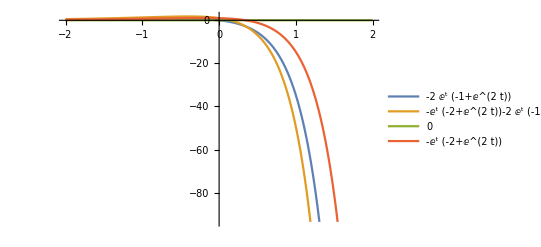

```mathematica
Plot[Evaluate[taby], {t,-2,2}, PlotLegends->"Expressions"]
```

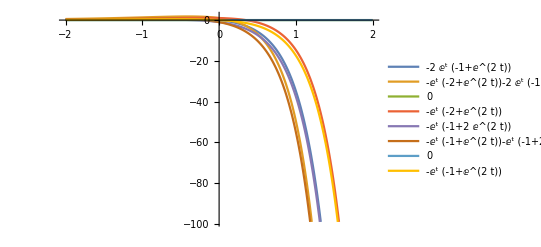

```mathematica
Plot[Evaluate[{taby, tabx}], {t,-2,2}, PlotLegends->"Expressions"]
```

## Ques 4 : dx/dt = 3x - 4y dy/dt= 2x-y

```mathematica
eq1={x'[t]==3*x[t]-4*y[t], y'[t]== -y[t] +2*x[t]}
```

{x'[t]==3 x[t]-4 y[t],y'[t]==2 x[t]-y[t]}

```mathematica
sol=DSolve[eq1, {y[t], x[t]}, t]
```

{{x[t]→-2 ⅇ^t C[2] Sin[2 t]+ⅇ^t C[1] (Cos[2 t]+Sin[2 t]),y[t]→ⅇ^t C[2] (Cos[2 t]-Sin[2 t])+ⅇ^t C[1] Sin[2 t]}}

```mathematica
tabx=Table[x[t]/.sol[[1,1]]/. {C[1]-> i, C[2]-> j}, {i,-2,0}, {j,0,2}]//Flatten
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i, C[2]-> j}, {i, -2, 0}, {j,0,2}]//Flatten
```

{-ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-ⅇ^(-4 t) (1+ⅇ^(2 t)),-ⅇ^(-4 t) (-1+ⅇ^(2 t))-ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),-ⅇ^(-4 t) (-1+ⅇ^(2 t))}

{ⅇ^(-4 t) (-1+ⅇ^(2 t)),ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),ⅇ^(-4 t) (-1+ⅇ^(2 t))+ⅇ^(-4 t) (1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+ⅇ^(-4 t) (1+ⅇ^(2 t)),0,1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),ⅇ^(-4 t) (1+ⅇ^(2 t))}

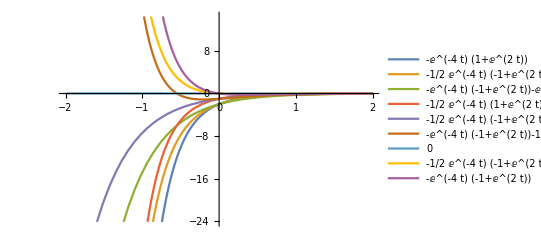

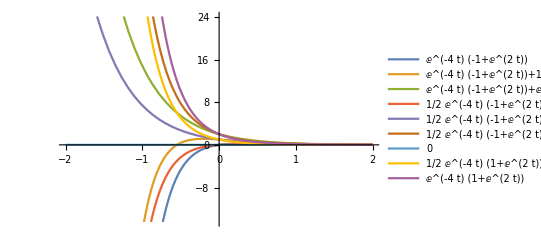

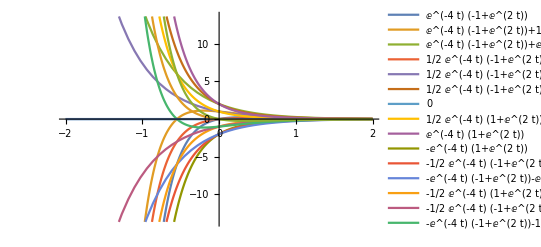

```mathematica
Plot[Evaluate[tabx], {t,-2,2}, PlotLegends->"Expressions"]
Plot[Evaluate[taby], {t,-2,2}, PlotLegends->"Expressions"]
Plot[Evaluate[{taby, tabx}], {t,-2,2}, PlotLegends->"Expressions"]
```

## Ques 5 : dx/dt = 2x + 7y dy/dt= 3x+2y with x[0]=9, y[0]=-1

{{x'[t]==2 x[t]+7 y[t],y'[t]==3 x[t]+2 y[t]},x[0]==9,y[0]==-1}

{{x[t]→-1/6 ⅇ^(2 t-√21 t) (-27-√21-27 ⅇ^(2 √21 t)+√21 ⅇ^(2 √21 t)),y[t]→1/14 ⅇ^(2 t-√21 t) (-7-9 √21-7 ⅇ^(2 √21 t)+9 √21 ⅇ^(2 √21 t))}}

{9/2 ⅇ^(2 t-√21 t)+1/2 √(7/3) ⅇ^(2 t-√21 t)+9/2 ⅇ^(2 t+√21 t)-1/2 √(7/3) ⅇ^(2 t+√21 t),-1/2 ⅇ^(2 t-√21 t)-9/2 √(3/7) ⅇ^(2 t-√21 t)-1/2 ⅇ^(2 t+√21 t)+9/2 √(3/7) ⅇ^(2 t+√21 t)}

9/2 ⅇ^(2 t-√21 t)+1/2 √(7/3) ⅇ^(2 t-√21 t)+9/2 ⅇ^(2 t+√21 t)-1/2 √(7/3) ⅇ^(2 t+√21 t)

-1/2 ⅇ^(2 t-√21 t)-9/2 √(3/7) ⅇ^(2 t-√21 t)-1/2 ⅇ^(2 t+√21 t)+9/2 √(3/7) ⅇ^(2 t+√21 t)

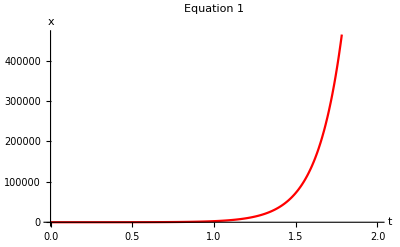

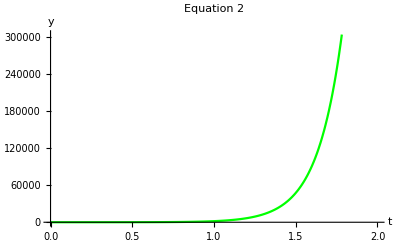

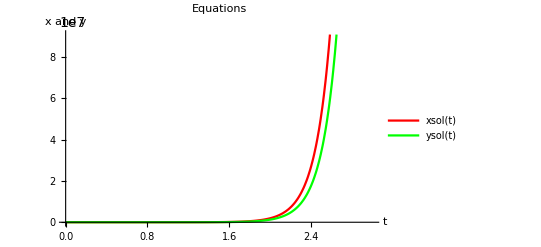

```mathematica
eq2={{x'[t]==7*y[t]+2*x[t], y'[t]==2*y[t]+3*x[t]}, x[0]==9, y[0]==-1}
DSolve[eq2, {x[t], y[t]}, t]
{xsol[t_], ysol[t_]}= ExpandAll[{x[t], y[t]}/.Flatten[DSolve[eq2, {x[t], y[t]}, t]]]
xsol[t]
ysol[t]
plot1=Plot[xsol[t], {t,0,2}, AxesLabel->{"t", "x"}, PlotLabel->"Equation 1", PlotStyle->{Red}]
plo2=Plot[ysol[t], {t,0,2}, AxesLabel->{"t", "y"}, PlotLabel->"Equation 2", PlotStyle->{Green}]
Plot[{xsol[t], ysol[t]}, {t,0,3}, AxesLabel->{"t","x and y" }, PlotLabel->"Equations", PlotStyle->{Red, Green}, PlotLegends->"Expressions"]
```

## Ques 6 : dx/dt = 7x - y dy/dt= 4x + 3y with initial conditions x[0]=1, y[0]=3

{{x'[t]==7 x[t]-y[t],y'[t]==4 x[t]+3 y[t]},x[0]==1,y[0]==3}

{{x[t]→-ⅇ^(5 t) (-1+t),y[t]→-ⅇ^(5 t) (-3+2 t)}}

{ⅇ^(5 t)-ⅇ^(5 t) t,3 ⅇ^(5 t)-2 ⅇ^(5 t) t}

ⅇ^(5 t)-ⅇ^(5 t) t

3 ⅇ^(5 t)-2 ⅇ^(5 t) t

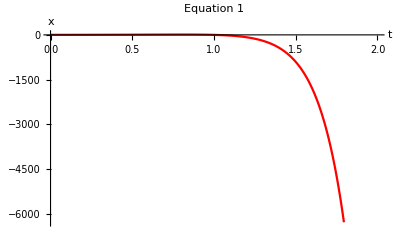

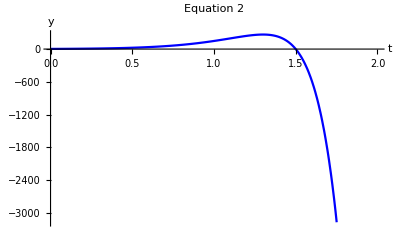

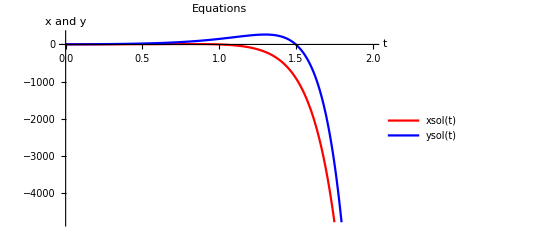

```mathematica
eq2={{x'[t]==-y[t]+7*x[t], y'[t]==3*y[t]+4*x[t]}, x[0]==1, y[0]==3}
DSolve[eq2, {x[t], y[t]}, t]
{xsol[t_], ysol[t_]}= ExpandAll[{x[t], y[t]}/.Flatten[DSolve[eq2, {x[t], y[t]}, t]]]
xsol[t]
ysol[t]
plot1=Plot[xsol[t], {t,0,2}, AxesLabel->{"t", "x"}, PlotLabel->"Equation 1", PlotStyle->{Red}]
plo2=Plot[ysol[t], {t,0,2}, AxesLabel->{"t", "y"}, PlotLabel->"Equation 2", PlotStyle->{Blue}]
Plot[{xsol[t], ysol[t]}, {t,0,2}, AxesLabel->{"t","x and y" }, PlotLabel->"Equations", PlotStyle->{Red, Blue}, PlotLegends->"Expressions"]
```